```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[StringDrop[NotebookDirectory[],-4]]
```

H:\2_Programming\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

### Import Data

```mathematica
quarkData = <<"output/yukawa_quark.m";
Print["Number of Yu Yd 3x3 matrix pairs"]
Dimensions[quarkData]
```

Number of Yu Yd 3x3 matrix pairs

{1321,2,3,3}

```mathematica
leptonData = <<"output/yukawa_lepton.m";
Print["Number of Yn Ye 3x3 matrix pairs (normal hierarchy)"]
Dimensions[leptonData[[1]]]
Print["Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)"]
Dimensions[leptonData[[2]]]
```

Number of Yn Ye 3x3 matrix pairs (normal hierarchy)

{4330,2,3,3}

Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)

{}

#### Loading necessary data

```mathematica
(* Import cL, cR calculated above *)
```

```mathematica
{cMArray,cuData,cdData,clNHData}=<<"output/cLcR02.m";
```

```mathematica
Dimensions/@{cuData,cdData,clNHData}
```

{{1321,41,3,2},{1321,41,3,2},{4330,41,3,2}}

```mathematica
(* Get A matrices from yu, yd data *)
```

```mathematica
quarkAData = Table[
yu = quarkData[[i, 1]]; yd = quarkData[[i,2]];myu=Minors[quarkData[[i, 1]]];myd=Minors[quarkData[[i, 2]]];
QuarkAMatrices[yu, yd, myu, myd]
,{i,Length[quarkData]}
];//AbsoluteTiming
Clear[yu,yd,myu,myd]
Dimensions[quarkAData]
```

{0.925294,Null}

{1321,4,3,3}

```mathematica
leptonADataNH = Table[
yn = leptonData[[1]][[i, 1]]; ye = leptonData[[1]][[i,2]];myn=Minors[yn];mye=Minors[ye];
LeptonAMatrices[yn, ye, myn, mye,1]
,{i,Length[leptonData[[1]]]}
];//AbsoluteTiming
Clear[yn,ye,myn,mye]
Dimensions[leptonADataNH]
```

{1.57847,Null}

{4330,2,3,3}

```mathematica
(* 
leptonADataIH = Table[
yn = leptonData[[2]][[i, 1]]; ye = leptonData[[2]][[i,2]];myn=Minors[yn];mye=Minors[ye];
LeptonAMatrices[yn, ye, myn, mye,2]
,{i,Length[leptonData[[2]]]}
];//AbsoluteTiming
Clear[yn,ye,myn,mye]
Dimensions[leptonADataIH]
*)
```

```mathematica
colors=ColorData[97,"ColorList"];
```

```mathematica
fvmin = 13.5;fvmax=17.5;
cvmin=-6;cvmax=-2;
```

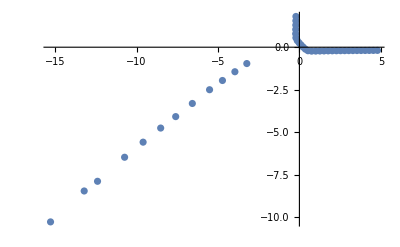

```mathematica
ListPlot[cuData[[10,All,1,All]]]
```